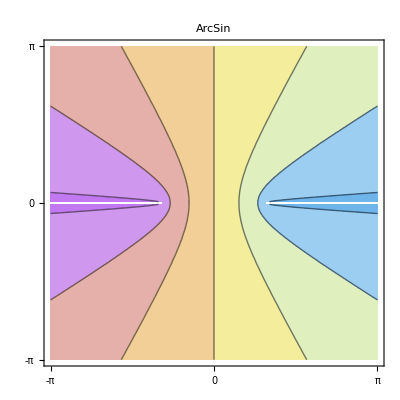
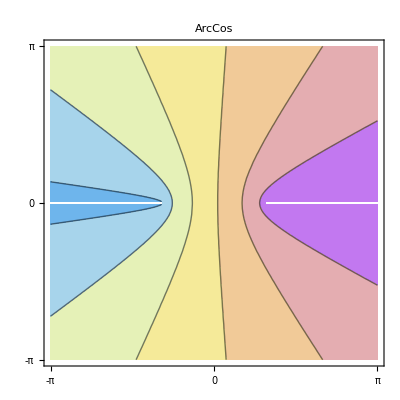
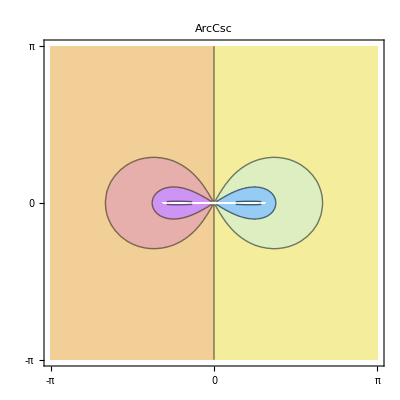
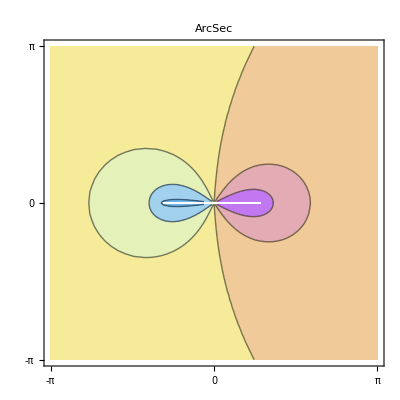
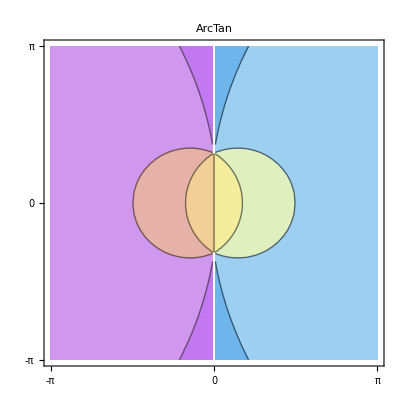
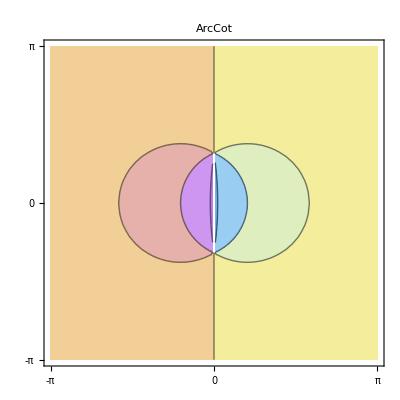

```mathematica
Table[
ContourPlot[
Re[f[x+I y]],{x,-Pi,Pi},{y,-Pi,Pi},PlotLabel->f,FrameTicks->{{-Pi,0,Pi},{-Pi,0,Pi}},ClippingStyle->Automatic,ColorFunction->"Pastel"
],
{f,{ArcSin,ArcCos,ArcCsc,ArcSec,ArcTan,ArcCot}}
]
```

418.964

0.937499

-0.937499

57.0545 x^2

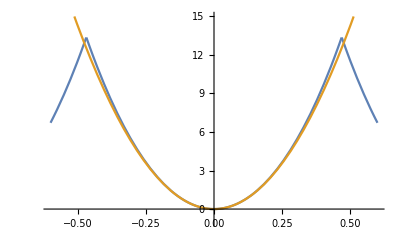

-Graphics-

-Graphics3D-

```mathematica
α={0.1,0.55,0.35};
β={6.0,1.2,0.3};
γ=α/β;

PesoAtomicoSilicio =28.0855; (*AMU, Nav atomi pesano 28.0855 grammi*)
DensitaMassaSilicio = 2.33*10^-6; (* g/m^3 *)
Navogadro=6.022140857*10^26;

Natomi=Navogadro / (PesoAtomicoSilicio/DensitaMassaSilicio) ;(* Atomi/m^3 *)
Upl[x_]:=1;
Zi=1; (*Numero di carica particella incidente*)
ZSi=14;(*Numero atomico silicio*)
e=1.60217646*10^-19;(*Coul*)
atf=0.8853*0.529 ZSi^(-1/3)(*(10^-10)*);(*Angstrom=10^-10 m*)
dp=2.35(*(10^-10)*); (*Big Interplanar distance of Si(111), [Ang]; Small one 0.78 Ang*)
ut=0.075(*(10^-10)*);(*Standard deviation at room temperature of gaussian atom displacement along one axis*)
τ=(β^2 ut^2)/(2 atf^2);
Upl[x_]:=2Pi Natomi dp Zi ZSi e^2 atf Sum[ γ[[i]]/2 Exp[τ[[i]]] * (Exp[(-β[[i]] x)/2 ] Erfc[1/(√2)((β[[i]] ut)/atf-x/ut)]+Exp[(β[[i]] x)/atf]Erfc[1/(√2)((β[[i]] ut)/atf+x/ut)]),{i,1,3}];
UplEv[x_]:=2Pi Natomi dp Zi ZSi     e     atf Sum[ γ[[i]]/2 Exp[τ[[i]]] * (Exp[(-β[[i]] x)/2 ] Erfc[1/(√2)((β[[i]] ut)/atf-x/ut)]+Exp[(β[[i]] x)/atf]Erfc[1/(√2)((β[[i]] ut)/atf+x/ut)]),{i,1,3}];
UplEv[1]
UtotEv[x_]=UplEv[dp/2-x]+UplEv[dp/2+x]-2UplEv[dp/2];
xmax=x/.Last[NMaximize[UtotEv[x],{x}∈Interval[{0,5}]]]
xmin=x/.Last[NMaximize[UtotEv[x],{x}∈Interval[{0,-5}]]]
UtotPer[x_]:=UtotEv[Mod[x,xmax,-xmax/2]];
(*PlotContorno = ContourPlot[Sin[Sqrt[(x)^2+(y)^2]],{x,0,4 Pi},{y,-4Pi,4 Pi},ContourShading->None,MaxRecursion->2,PlotPoints->100][[1]];*)
(*PlotContorno2 = ContourPlot[Sin[Sqrt[(x)^2+(y)^2]],{x,-4Pi,4 Pi},{y,-20Pi,-12Pi},ContourShading->None,MaxRecursion->2,PlotPoints->100][[1]];*)
(*DensityPlot[Sin[Sqrt[(x)^2+(y)^2]],{x,0,4 Pi},{y,-4Pi,4 Pi},ColorFunction->"Pastel",MaxRecursion->2,PlotPoints->100, Epilog->{PlotContorno2}]*)
QuadApproxUtot[x_]=Normal[Series[UtotEv[x],{x,0,4}]]
Plot[{UtotPer[x],QuadApproxUtot[x]},{x,-0.6,0.6}, PlotRange->{-1,15}]
(*ReliefPlot[Table[Sin[Sqrt[(x)^2+(y)^2]],{x,-4Pi,4 Pi,0.05},{y,-20Pi,-12Pi,0.05}],ColorFunction->"SolarColors"]*)
(*ReliefPlot[Table[UtotPer[y],{x,-dp,dp,0.01},{y,-dp,dp,0.01}],ColorFunction->"SolarColors"]*)
ReliefPlot[Table[UtotPer[Sqrt[x^2+(y-20)^2]],{x,-dp,dp,0.01},{y,-dp,dp,0.01}],ColorFunction->"SolarColors",FrameTicks->True,PerformanceGoal->"Quality", Epilog->gp]
(*Plot3D[UtotPer[x],{x,-dp,dp},{y,-5,5},Mesh->None,ColorFunction->"SolarColors"]*)
Plot3D[UtotPer[Sqrt[x^2+(y-20)^2]],{x,-dp,dp},{y,-dp,dp},Mesh->None,ColorFunction->"SolarColors",MaxRecursion->2,PlotPoints->50]
```

```mathematica
CurrencyConvert[Quantity[100,"SwissFrancs"],"Euros"]
```

92.17 €

```mathematica
x/.Last[NMaximize[UtotEv[x],x]]
```

0.937499

```mathematica
Series[UtotEv[x],{x,0,4}]
```

57.0545 x^2+16.4509 x^4+O[x]^5

```mathematica
ht = QuantityMagnitude[Quantity["PlanckConstant"],"Joules*Seconds"];
ProtMass = QuantityMagnitude[Quantity["ProtonMass"],"Kilograms"];
EletMass = QuantityMagnitude[Quantity["ElectronMass"],"Kilograms"];
speedlight=QuantityMagnitude[Quantity["SpeedOfLight"],"m/s"];
momentum = p*ec (*GeV*);
vpart=(speedlight2 momentum)/(√(speedlight2^2 EletMass2^2+momentum^2))
gamma =1/(√(1-vpart^2/speedlight2^2))
dp2/(ht2 √8)√(U0*EletMass2*gamma)
N[dp2/(ht2 √8)√(U0*EletMass2*gamma),40]/.{dp2->dp,ht2->ht,U0->20e,EletMass2->EletMass,ec->e,p->10,speedlight2->speedlight}
```

(ec p speedlight2)/(√(ec^2 p^2+EletMass2^2 speedlight2^2))

1/(√(1-(ec^2 p^2)/(ec^2 p^2+EletMass2^2 speedlight2^2)))

(dp2 √((EletMass2 U0)/(√(1-(ec^2 p^2)/(ec^2 p^2+EletMass2^2 speedlight2^2)))))/(2 √2 ht2)

1.6409×10^11

6.62607×10^-34

1.672622×10^-27

9.109383×10^-31

2.14231×10^9

```mathematica
UnitConvert[Quantity[1,"Electronvolts"],"Joules"]
```

1.602177×10^-19 J

```mathematica
Series[UtotEv[x],{x,0,4}]
```

57.0545 x^2+16.4509 x^4+O[x]^5

```mathematica
Normal[57.05445712227877 x^2+O[x]^3]
```

57.0545 x^2

```mathematica
Normal[Series[UtotEv[x],{x,0,2}]]
```

57.0545 x^2

```mathematica
Solve[1/Sqrt[1-v^2/c^2] m*v==p,v]
```

{{v→-(c p)/(√(c^2 m^2+p^2))},{v→(c p)/(√(c^2 m^2+p^2))}}

```mathematica
Epilog
```

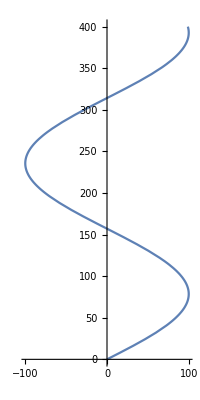

```mathematica
ParametricPlot[{100Sin[0.02u],u},{u,0,400}]
```

```mathematica
gp = First[ParametricPlot[{100Sin[0.02u],u},{u,0,400}]];
```

```mathematica
QuadApproxUtot[0.425]-
```

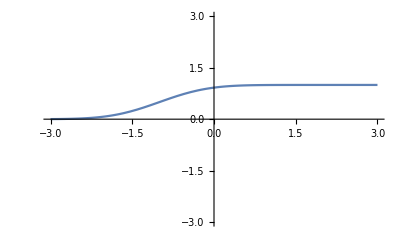

```mathematica
Plot[1/2Erf[1(x+1)]+1/2,{x,-3,3}, PlotRange->{-3,3}]
```

```mathematica
|
```